

```mathematica
Plot[x,{x,-2,2}]
```

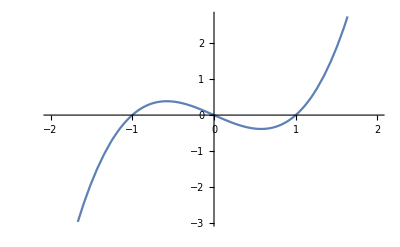

```mathematica
Plot[x^3-x,{x,-2,2}]
```

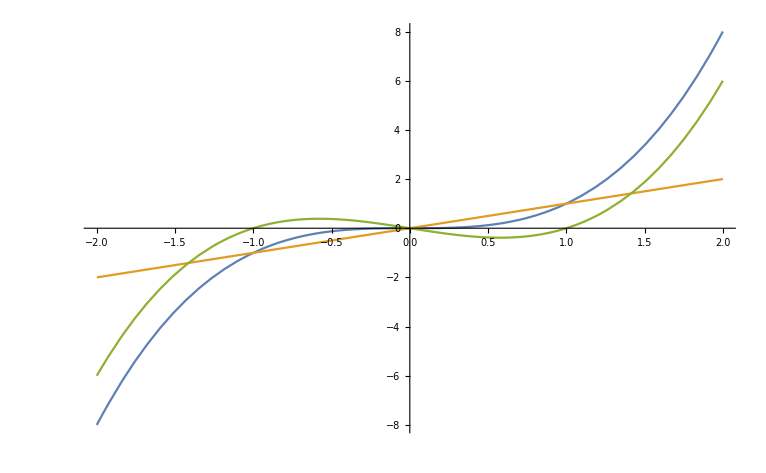

```mathematica
Plot[{x^3,x,x^3-x},{x,-2,2}]
```

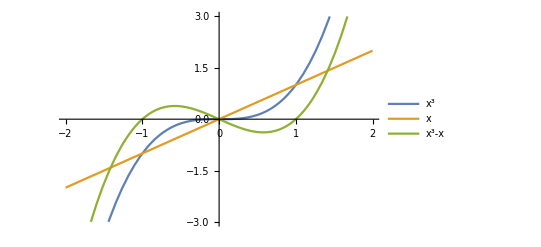

```mathematica
Plot[{x^3,x,x^3-x},{x,-2,2},PlotLegends->"Expressions",PlotRange->{{-2,2},{-3,3}}]
```

```mathematica
Plot[{x^3,-x,x^3-x},{x,-2,2},PlotLegends->"Expressions",PlotRange->{{-2,2},{-3,3}}]
```

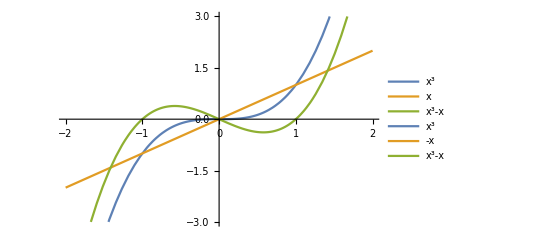

```mathematica
Plot[{x^3,x,x^3-x},{x,-2,2},PlotLegends->"Expressions",PlotRange->{{-2,2},{-3,3}}]
```

```mathematica
|
```

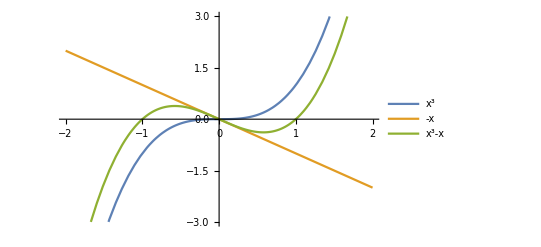

```mathematica
Plot[{x^3,-x,x^3-x},{x,-2,2},PlotLegends->"Expressions",PlotRange->{{-2,2},{-3,3}}]
```

```mathematica
FullSimplify[Normalize@{x,x^3-x}.Normalize@{x,-x},x∈Reals]
```

-(-2+x^2)/(√2 √(2-2 x^2+x^4))

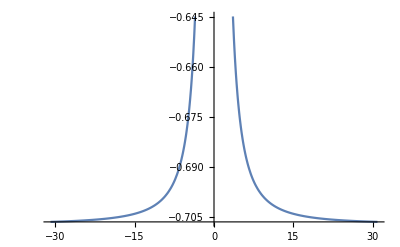

```mathematica
Plot[-(-2+x^2)/(√2 √(2-2 x^2+x^4)),{x,-30.886424202228397,30.886424202228397}]
```

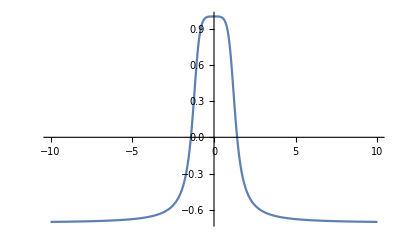

```mathematica
Plot[-(-2+x^2)/(√2 √(2-2 x^2+x^4)),{x,-10,10},PlotRange->Full]
```

```mathematica
Manipulate[
Integrate[(-2+x^2)/(√2 √(2-2 x^2+x^4)),{x,-a,a}]
,{a,.001,5}]
```

```mathematica
Manipulate[
NIntegrate[(-2+x^2)/(√2 √(2-2 x^2+x^4)),{x,-a,a}]
,{a,.001,5}]
```